```mathematica
(* Run 2_H3_Calculation_of_objects first! *)
```

# Calculation of the ABC-equation for perfect tangles in Haagerup

## Definitions

## Install TriCat package by Stiegemann and load adjacency matrices and relations for morphisms in C_6

```mathematica
(*Install Library for trivalent Categories*)
SetDirectory[NotebookDirectory[]];
<<TriCats`;
(*Load Elements from C4 of a cubic trivalent category*)
LoadLibrary["stdlib"]
C4=Retrieve["C4Atoms"];
```

```mathematica
ip61=Import[FileNameJoin[{NotebookDirectory[],"ip61.m"}]];
ip62=Import[FileNameJoin[{NotebookDirectory[],"ip62.m"}]];
nullspace62=Import[FileNameJoin[{NotebookDirectory[],"nullspace62.m"}]];
C61=Import[FileNameJoin[{NotebookDirectory[],"C61.m"}]];
C62=Import[FileNameJoin[{NotebookDirectory[],"C62.m"}]];
```

## Define basis, operators and parameters

```mathematica
(*Define function which moves legs of every Diagram in a list of diagrams down*)
DiagramsMoveAllDown[diagramList_,newIngoingLegs_]:=Module[{MovedDiagramList},
MovedDiagramList={};
For[i=1,i≤Length[diagramList],i++,MovedDiagramList=AppendTo[MovedDiagramList,DiagramMoveDown[diagramList[[i]],newIngoingLegs]]];
Return[MovedDiagramList]
]
```

```mathematica
(*Define Basis of C4 of cubic trivalent category*)
C4Basis=DiagramsMoveAllDown[C4,2][[1;;4]];
```

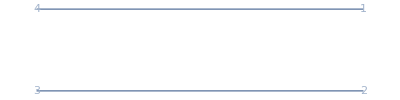
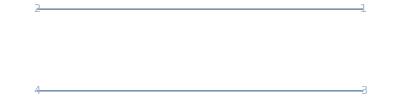
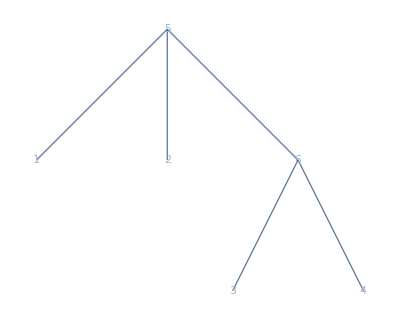
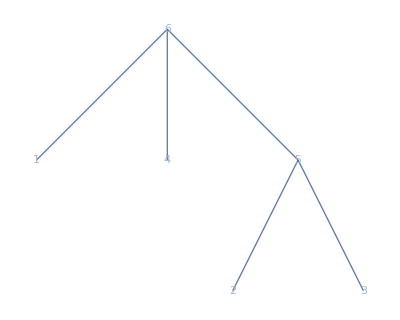
{Diagram[-Graphics-,{4,3},{1,2}],Diagram[-Graphics-,{4,3},{1,2}],Diagram[-Graphics-,{4,3},{1,2}],Diagram[-Graphics-,{4,3},{1,2}]}

```mathematica
EnsureGraph[C4Basis]
```

```mathematica
(*Define operators in basis representation*)
Clear[a1,a2,a3,a4,b1,b2,b3,b4,c1,c2,c3,c4,d1,d2,d3,d4,t1,t2,t3,t4];
OpA=a1*C4Basis[[1]]+a2*C4Basis[[2]]+a3*C4Basis[[3]]+a4*C4Basis[[4]];
OpB=b1*C4Basis[[1]]+b2*C4Basis[[2]]+b3*C4Basis[[3]]+b4*C4Basis[[4]];
OpC=c1*C4Basis[[1]]+c2*C4Basis[[2]]+c3*C4Basis[[3]]+c4*C4Basis[[4]];
OpD=d1*C4Basis[[1]]+d2*C4Basis[[2]]+d3*C4Basis[[3]]+d4*C4Basis[[4]];
OpT=t1*C4Basis[[1]]+t2*C4Basis[[2]]+t3*C4Basis[[3]]+t4*C4Basis[[4]]/.{t1->4/Sqrt[3],t2->d/Sqrt[3]-I*Sqrt[5-d],t4->-2*Sqrt[3](d+1)+2*I*Sqrt[5*d+2],t3->-3*Sqrt[3]*d+I*Sqrt[5-d]};
```

```mathematica
(*Definition of the parameters of the trivalent category. Here: Hagerup*)
bigon=1;
loop=(3+√13)/2;
triangle=-2/3 loop+5/3;
```

```mathematica
(*Define basis for C6 in Hagerup*)
C6Basis=Delete[C61,{{38},{39},{40},{41}}];
```

## Define function which replaces linear dependent diagrams in C(6,2) by corresponding basis representation

```mathematica
(*This function replaces all diagrams which are no basis elements of C6 by a linear combination of C6's basis elements*)
ReplaceKernDiagrams[diagram_]:=Module[{KernDiagrams,KernDiagramsInOut,DiagramList,ingoingLegs,ReplacementRules,ReplacedDiagramList,ReplacedDiagram,NormalDiagramList,DistinctList,ReplaceWrongForm},
DiagramList=List@@ExpandAll[diagram];
ingoingLegs=Length[DistinctDiagrams[List@@diagram][[1]][[2]]];
KernDiagrams=C62[[Length[C6Basis]+1;;Length[C62]]];
KernDiagramsInOut=DiagramsMoveAllDown[KernDiagrams,ingoingLegs];
ReplacementRules=KernDiagramsInOut;
For[i=1,i≤Length[KernDiagramsInOut],i++,ReplacementRules=ReplacePart[ReplacementRules,i->(KernDiagramsInOut[[i]]->(Sum[nullspace62[[i]][[j]]*DiagramMoveDown[C6Basis[[j]],ingoingLegs],{j,Length[C6Basis]}]) )]];
DistinctList={};
For[i=1,i≤Length[DiagramList],i++,DistinctList=AppendTo[DistinctList,DeleteCases[List@@DiagramList[[i]],Except[_Diagram]][[1]]]];
DistinctList=DeleteDuplicates[DistinctList];
ReplaceWrongForm={};
For[i=1,i≤Length[DistinctList],i++,For[j=1,j≤Length[KernDiagramsInOut],j++,If[IsomorphicDiagramQ[DistinctList[[i]],KernDiagramsInOut[[j]]]==True,ReplaceWrongForm=AppendTo[ReplaceWrongForm,DistinctList[[i]]->KernDiagramsInOut[[j]]]]]];
NormalDiagramList=DiagramList/.ReplaceWrongForm;
ReplacedDiagramList=NormalDiagramList/.ReplacementRules;
ReplacedDiagram=Total[ReplacedDiagramList];
Return[ReplacedDiagram]
];
```

## Calculations

## Calculate the case Tangle4 = Tangle0 to get a solution for A in terms of the other parameters

```mathematica
(*Definition of the case where tangle intersects all four legs*)
Tangle4=ReduceDiagram[
DiagramCompose[
DiagramTensor[Retrieve["Line"],Retrieve["Cup"],Retrieve["Line"]],
DiagramCompose[
DiagramTensor[OpA,OpD],
DiagramCompose[
DiagramTensor[Retrieve["Line"],OpT,Retrieve["Line"]],
DiagramCompose[
DiagramTensor[OpB,OpC],
DiagramTensor[Retrieve["Line"],Retrieve["Cap"],Retrieve["Line"]]
]
]
]
]
,b->bigon,d-> loop,t-> triangle];
```

```mathematica
(*Calculate Solution*)
T4Comp=Components[Tangle4,C4Basis]/.d->loop;
TComp=Components[OpT,C4Basis]/.d->loop;
```

```mathematica
SolutionA=Solve[T4Comp==TComp*loop,{a1,a2,a3,a4}];
```

```mathematica
a1Sol=SolutionA[[1,1,2]]
```

-((((((b4 c4 d3 AlgebraicNumber0.204AlgebraicNumber[√13,{-344/81,100/81}]0.20438429069628286)/(√3)+(b4 c3 d4 AlgebraicNumber0.204AlgebraicNumber[√13,{-344/81,100/81}]0.20438429069628286)/(√3)+154+b4 c4 d4 AlgebraicNumber-0.0170AlgebraicNumber[√13,{86/243,-25/243}]-0.01703202422469024 (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+2 ⅈ √(AlgebraicNumber18.5AlgebraicNumber[√13,{19/2,5/2}]18.513878188659973))+b2 c2 d4 AlgebraicNumber-0.535AlgebraicNumber[√13,{2/3,-1/3}]-0.5351837584879964 (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+2 ⅈ √(AlgebraicNumber18.5AlgebraicNumber[√13,{19/2,5/2}]18.513878188659973))) (1)-(1/(√3)+148+1) 1) 1-1) 1-1)/((1) ((((b4 c4 d3 AlgebraicNumber0.204AlgebraicNumber[√13,{-344/81,100/81}]0.20438429069628286)/(√3)+(b4 c3 d4 AlgebraicNumber0.204AlgebraicNumber[√13,{-344/81,100/81}]0.20438429069628286)/(√3)+154+b4 c4 d4 AlgebraicNumber-0.0170AlgebraicNumber[√13,{86/243,-25/243}]-0.01703202422469024 (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+2 ⅈ √(AlgebraicNumber18.5AlgebraicNumber[√13,{19/2,5/2}]18.513878188659973))+b2 c2 d4 AlgebraicNumber-0.535AlgebraicNumber[√13,{2/3,-1/3}]-0.5351837584879964 (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+2 ⅈ √(AlgebraicNumber18.5AlgebraicNumber[√13,{19/2,5/2}]18.513878188659973))) (1/(√3)+156+1)-1) 1-1)-1))
 |  |  |  |

```mathematica
Export["a1Sol.m",a1Sol];
```

```mathematica
a2Sol=SolutionA[[1,2,2]]
```

-(((((b4 c4 d3 AlgebraicNumber0.204AlgebraicNumber[√13,{-344/81,100/81}]0.20438429069628286)/(√3)+(b4 c3 d4 AlgebraicNumber0.204AlgebraicNumber[√13,{-344/81,100/81}]0.20438429069628286)/(√3)+(b4 c4 d4 AlgebraicNumber-0.0888AlgebraicNumber[√13,{-274/81,74/81}]-0.08875562488475068)/(√3)+153+b4 c4 d4 AlgebraicNumber-0.0170AlgebraicNumber[√13,{86/243,-25/243}]-0.01703202422469024 (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+2 ⅈ √(AlgebraicNumber18.5AlgebraicNumber[√13,{19/2,5/2}]18.513878188659973))+b2 c2 d4 AlgebraicNumber-0.535AlgebraicNumber[√13,{2/3,-1/3}]-0.5351837584879964 (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+2 ⅈ √(AlgebraicNumber18.5AlgebraicNumber[√13,{19/2,5/2}]18.513878188659973))) ((4 2 d1)/(√3)+156+1)-1) (1)-1)/((((b4 c4 d3 AlgebraicNumber0.204AlgebraicNumber[√13,{-344/81,100/81}]0.20438429069628286)/(√3)+(b4 c3 d4 AlgebraicNumber0.204AlgebraicNumber[√13,{-344/81,100/81}]0.20438429069628286)/(√3)+(b4 c4 d4 AlgebraicNumber-0.0888AlgebraicNumber[√13,{-274/81,74/81}]-0.08875562488475068)/(√3)+153+b4 c4 d4 AlgebraicNumber-0.0170AlgebraicNumber[√13,{86/243,-25/243}]-0.01703202422469024 (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+2 ⅈ √(AlgebraicNumber18.5AlgebraicNumber[√13,{19/2,5/2}]18.513878188659973))+b2 c2 d4 AlgebraicNumber-0.535AlgebraicNumber[√13,{2/3,-1/3}]-0.5351837584879964 (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+2 ⅈ √(AlgebraicNumber18.5AlgebraicNumber[√13,{19/2,5/2}]18.513878188659973))) ((4 2 d1)/(√3)+156+1)-1) (1)-1))+1/1
 |  |  |  |

```mathematica
Export["a2Sol.m",a2Sol];
```

```mathematica
a3Sol=SolutionA[[1,3,2]]
```

-((AlgebraicNumber-3.30AlgebraicNumber[√13,{-3/2,-1/2}]-3.302775637731995 ((AlgebraicNumber3.30AlgebraicNumber[√13,{3/2,1/2}]3.302775637731995)/(√3)-ⅈ √(AlgebraicNumber1.70AlgebraicNumber[√13,{7/2,-1/2}]1.6972243622680054)) ((4 b2 c1 d1)/(√3)+(4 b4 c1 d1)/(√3)+(b3 c4 d3 AlgebraicNumber0.204AlgebraicNumber[√13,{-344/81,100/81}]0.20438429069628286)/(√3)+152+b2 c1 d1 AlgebraicNumber-0.535AlgebraicNumber[√13,{2/3,-1/3}]-0.5351837584879964 (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+2 ⅈ √(AlgebraicNumber18.5AlgebraicNumber[√13,{19/2,5/2}]18.513878188659973))+b4 c1 d1 AlgebraicNumber-0.535AlgebraicNumber[√13,{2/3,-1/3}]-0.5351837584879964 (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+2 ⅈ √(AlgebraicNumber18.5AlgebraicNumber[√13,{19/2,5/2}]18.513878188659973))+b3 c1 d1 AlgebraicNumber0.286AlgebraicNumber[√13,{17/9,-4/9}]0.28642165534933817 (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+2 ⅈ √(AlgebraicNumber18.5AlgebraicNumber[√13,{19/2,5/2}]18.513878188659973)))+1/(√3))/(((b4 c4 d3 AlgebraicNumber0.204AlgebraicNumber[√13,{-344/81,100/81}]0.20438429069628286)/(√3)+(b4 c3 d4 AlgebraicNumber0.204AlgebraicNumber[√13,{-344/81,100/81}]0.20438429069628286)/(√3)+(b4 c4 d4 AlgebraicNumber-0.0888AlgebraicNumber[√13,{-274/81,74/81}]-0.08875562488475068)/(√3)+152+b4 c4 d3 AlgebraicNumber7.40 × 10^-3AlgebraicNumber[√13,{137/486,-37/486}]0.007396302073729223 (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+2 ⅈ √(AlgebraicNumber18.5AlgebraicNumber[√13,{19/2,5/2}]18.513878188659973))+b4 c4 d4 AlgebraicNumber-0.0170AlgebraicNumber[√13,{86/243,-25/243}]-0.01703202422469024 (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+2 ⅈ √(AlgebraicNumber18.5AlgebraicNumber[√13,{19/2,5/2}]18.513878188659973))+b2 c2 d4 AlgebraicNumber-0.535AlgebraicNumber[√13,{2/3,-1/3}]-0.5351837584879964 (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+2 ⅈ √(AlgebraicNumber18.5AlgebraicNumber[√13,{19/2,5/2}]18.513878188659973))) (1)-1))+1/1+1/(1-1)
 |  |  |  |

```mathematica
Export["a3Sol.m",a3Sol];
```

```mathematica
a4Sol=SolutionA[[1,4,2]]
```

(√3 AlgebraicNumber4.40AlgebraicNumber[√13,{2,2/3}]4.403700850309326)/((4 b2 c1 d1)/(√3)+(4 b4 c1 d1)/(√3)+√3 b3 c4 d3 AlgebraicNumber0.0681AlgebraicNumber[√13,{-344/243,100/243}]0.06812809689876095+√3 b3 c3 d4 AlgebraicNumber0.0681AlgebraicNumber[√13,{-344/243,100/243}]0.06812809689876095+151+b2 c1 d1 AlgebraicNumber-0.535AlgebraicNumber[√13,{2/3,-1/3}]-0.5351837584879964 (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+2 ⅈ √(AlgebraicNumber18.5AlgebraicNumber[√13,{19/2,5/2}]18.513878188659973))+b4 c1 d1 AlgebraicNumber-0.535AlgebraicNumber[√13,{2/3,-1/3}]-0.5351837584879964 (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+2 ⅈ √(AlgebraicNumber18.5AlgebraicNumber[√13,{19/2,5/2}]18.513878188659973))+b3 c1 d1 AlgebraicNumber0.286AlgebraicNumber[√13,{17/9,-4/9}]0.28642165534933817 (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+2 ⅈ √(AlgebraicNumber18.5AlgebraicNumber[√13,{19/2,5/2}]18.513878188659973)))+1/1+1+((1) (((1) (AlgebraicNumber-3.30AlgebraicNumber[√13,{-3/2,-1/2}]-3.302775637731995 (1) (√3 AlgebraicNumber-8.61AlgebraicNumber[√13,{-5,-1}]-8.60555127546399+1)+1)-1) (1)-1))/((-(1) (((4 b2 c1 d1)/(√3)+157) (1/(√3)+205+1/(√3))-1)+1) (1)-1)
 |  |  |  |

```mathematica
Export["a4Sol.m",a4Sol];
```

## Calculate the case Tangle3 = Tangle1

```mathematica
(*Definition of the case where tangle intersects 3 legs*)
Tangle3=ReduceDiagram[
DiagramCompose[
DiagramTensor[OpA,Retrieve["Line"],Retrieve["Line"]],
DiagramCompose[
DiagramTensor[Retrieve["Line"],OpT,Retrieve["Line"]],
DiagramCompose[
DiagramTensor[OpB,OpC],
DiagramTensor[Retrieve["Line"],Retrieve["Cap"],Retrieve["Line"]]
]
]
]
,{b->bigon,t-> triangle,d-> loop}];
```

```mathematica
(*Definition of the case where tangle intersects 1 leg*)
Tangle1=ReduceDiagram[
DiagramCompose[
DiagramTensor[Retrieve["Line"],OpD,Retrieve["Line"]],
DiagramCompose[
DiagramTensor[OpT,Retrieve["Line"],Retrieve["Line"]],
DiagramTensor[Retrieve["Line"],Retrieve["Line"],Retrieve["Cap"]]
]
]
,{b->bigon,t-> triangle,d-> loop}];
```

```mathematica
(*Calculate solution*)
T1Comp=Components[ReplaceKernDiagrams[Tangle1],DiagramsMoveAllDown[C6Basis,4]]/.d->loop;
T3Comp=Components[ReplaceKernDiagrams[Tangle3],DiagramsMoveAllDown[C6Basis,4]]/.d->loop;
```

```mathematica
T3Comp=Simplify[T3Comp];
T3Comp=FullSimplify[T3Comp];
```

```mathematica
Export["T1Comp_Trep.m",T1Comp];
Export["T3Comp_simpl_Trep.m",T3Comp];
```

```mathematica
Solve[T1Comp==T3Comp/.{a1->a1Sol//N,a2->a2Sol//N,a3->a3Sol//N,a4->a4Sol//N},{b1,b2,b3,b4,c1,c2,c3,c4,d1,d2,d3,d4}]
```

$Aborted

## Calculate the case Tangle2AD = Tangle2BC

```mathematica
(*Definition of the case where tangle intersects the 2 lower legs*)
Tangle2AD=ReduceDiagram[
DiagramCompose[
DiagramTensor[Retrieve["Line"],Retrieve["Cup"],Retrieve["Line"]],
DiagramCompose[
DiagramTensor[OpA,OpD],
DiagramTensor[Retrieve["Line"],OpT,Retrieve["Line"]]
]
]
,b->bigon,d-> loop,t-> triangle];
```

```mathematica
(*Definition of the case where tangle intersects the 2 upper legs*)
Tangle2BC=ReduceDiagram[
DiagramCompose[
DiagramTensor[Retrieve["Cup"],Retrieve["Line"],Retrieve["Line"],Retrieve["Cup"]],
DiagramCompose[
DiagramTensor[Retrieve["Line"],Retrieve["Line"],OpT,Retrieve["Line"],Retrieve["Line"]],
DiagramCompose[
DiagramTensor[Retrieve["Line"],OpB,OpC,Retrieve["Line"]],
DiagramTensor[Retrieve["Line"],Retrieve["Line"],Retrieve["Cap"],Retrieve["Line"],Retrieve["Line"]]
]
]
]
,b->bigon,d-> loop,t-> triangle];
```

```mathematica
(*Calculate solution*)
T2ADComp=Components[ReplaceKernDiagrams[Tangle2AD],DiagramsMoveAllDown[C6Basis,2]]/.d->loop;
T2BCComp=Components[ReplaceKernDiagrams[Tangle2BC],DiagramsMoveAllDown[C6Basis,2]]/.d->loop;
```

```mathematica
T2ADComp=Simplify[T2ADComp];
T2ADComp=FullSimplify[T2ADComp];
T2BCComp=Simplify[T2BCComp];
T2BCComp=FullSimplify[T2BCComp];
```

```mathematica
Export["T2ADComp_Trep.m",T2ADComp];
Export["T2BCComp_Trep.m",T2BCComp];
```

```mathematica
Solve[T2ADComp==T2BCComp,{b1,b2,b3,b4}]
```

{}

## Calculate whether there is a solution to the equations

```mathematica
(*Import files in case you do not want to calculate the code before*)
T3Comp=Import[FileNameJoin[{NotebookDirectory[],"T3Comp_Simplified.m"}]];
T1Comp=Import[FileNameJoin[{NotebookDirectory[],"T1Comp.m"}]];
T2ADComp=Import[FileNameJoin[{NotebookDirectory[],"T2ADComp.m"}]];
T2BCComp=Import[FileNameJoin[{NotebookDirectory[],"T2BCComp.m"}]];
```

```mathematica
(*Function which checks one specific "Component" of TxComp and searches for the pre-factor of "Wert" in this specific Component*)
Search[Tangle_,Wert_,Component_]:=Module[
{iList,iListString,MatrixEntry,Val,iListj,c,Header},
Header=Head[ExpandAll[Tangle[[Component]]]];
If[
Header===Plus,
iList=List@@ExpandAll[Tangle[[Component]]],
iList={Tangle[[Component]]}
];(*If*)
MatrixEntry={};
For[j=1,j≤Length[iList],j++,
iListj=ExpandAll[iList[[j]]];
If[StringContainsQ[ToString[iListj],ToString[Wert]]==True,
If[StringContainsQ[ToString[iListj],"--"],

Val=iListj//ToString[#,InputForm]&//StringReplace[#,"/":>"--"]&;
Val=StringDelete[Val,ToString[Wert]<>"*"];
Val=Val//StringReplace[#,"--":>"/"]&//ToExpression[#,InputForm]&;
MatrixEntry=AppendTo[MatrixEntry,Val],
Val=StringDelete[ToString[iList[[j]]],ToString[Wert]];
Val=ToExpression[Val];
MatrixEntry=AppendTo[MatrixEntry,Val];
](*If*)
,MatrixEntry=AppendTo[MatrixEntry,0]](*If*)
];(*For*)
If[Header===Integer,MatrixEntry=0,MatrixEntry=Header@@MatrixEntry];
Return[MatrixEntry]
](*Module*)
```

```mathematica
(*Funcion which gives out every non-numerical parameter in TxComp*)
Parameters[Tangle_]:=Module[{DummieList,ComponentList,VariableList,i},
(*Find out occuring variables*)
DummieList=List@@ExpandAll[Plus@@Tangle];
ComponentList=List@@Times@@Sum[Plus@@DummieList[[i]],{i,1,Length[DummieList]}];
VariableList={};
For[i=1,i≤Length[ComponentList],i++,
If[Head[ComponentList[[i]]]==Symbol,VariableList=AppendTo[VariableList,ComponentList[[i]]]
](*If*)
](*For*);
Return[VariableList]
](*Module*)
```

```mathematica
(*Creates matrix for system of linear equations out of a vector*)
LinEqMatrix[Tangle_]:=Module[{VariableList,EntryList,Matrix,j,i},
VariableList=DeleteCases[DeleteCases[DeleteCases[DeleteCases[Parameters[Tangle],t1],t2],t3],t4];
Matrix={};
EntryList={};
For[i=1,i≤Length[Tangle],i++,
For[j=1,j≤Length[VariableList],j++,
EntryList=AppendTo[EntryList,Search[Tangle,VariableList[[j]],i]];
](*For*);
Matrix=AppendTo[Matrix,EntryList];
EntryList={};
](*For*);
Return[Matrix]
](*Module*)
```

```mathematica
(*Calculate augmented matrix*)
CreateMatrix[Matrix1_,Tangle2_]:=Module[{i,Matrix,Entry},
If[Length[Matrix1]==Length[Tangle2],
Matrix=Matrix1;
For[i=1,i≤Length[Tangle2],i++,
Entry=AppendTo[Matrix[[i]],Tangle2[[i]]];
Matrix=ReplacePart[Matrix,i-> Entry]
](*For*)
,Print["not possible"]
](*If*);
Return[Matrix]
](*Module*)
```

```mathematica
T1Matrix=LinEqMatrix[T1Comp//N];
CoeffMatrix13=CreateMatrix[T1Matrix,T3Comp];
```

```mathematica
MatrixRank[T1Matrix]
```

0

```mathematica
MatrixRank[CoeffMatrix13]
```

1

```mathematica
T2ADMatrix=LinEqMatrix[T2ADComp];
CoeffMatrix22=CreateMatrix[T2ADMatrix,T2BCComp];
```

```mathematica
MatrixRank[T2ADMatrix]
```

7

```mathematica
MatrixRank[CoeffMatrix22]
```

8